# Analysis of data obtained with VASP

Milagros Delgado^1, Jhon Aponte^2, Matías Romero^2, Rolando Sánchez^1, and Andrés Toledo^1
[1] School of Physical Sciences and Nanotechnology, Yachay Tech University, Urcuquí - Ecuador
[2] School of Chemical Sciences and Engineering,  Yachay Tech University, Urcuquí - Ecuador

## Al

```mathematica
wrk = "/home/rolando/Downloads/Yachay/8th_Semester/dft/dft_coursework/midterm/MidTerm Challenge proyect/al-files/results";
SetDirectory[wrk];
```

### Analysis of ENCUT

```mathematica
dataal = Import["ecut.dat"];
dataal//TableForm
```

250 | -3.77047
300 | -3.77556
350 | -3.77841
400 | -3.77907
450 | -3.77943
500 | -3.77947
550 | -3.77949
600 | -3.77954
650 | -3.7796
700 | -3.77963
750 | -3.77965
800 | -3.77965
850 | -3.77966
900 | -3.77968

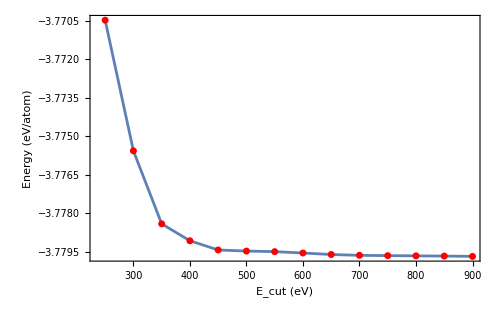

```mathematica
dataal //ListPlot[#,
Frame ->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

Let our convergence criteria to be 1 meV/atom

Using the criteria, let’s obtain a convergence window to find the E_cut

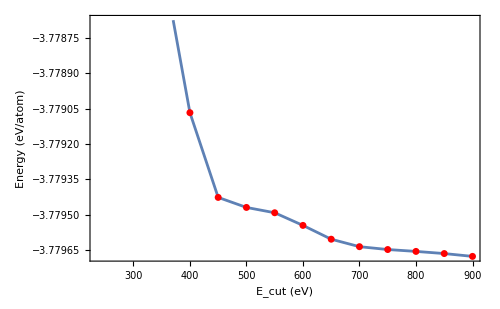

```mathematica
dataal //ListPlot[#,
Frame ->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->{#[[-1,2]],#[[-1,2] ]+10^-3},
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

ECUT = 400

### Analysis of k-points

```mathematica
datakp = Import["kps.dat"][[All, 1;;2]];
datakp//TableForm
```

15 | -3.74157
16 | -3.74576
17 | -3.74664
18 | -3.74583
19 | -3.74372
20 | -3.74461
21 | -3.74588
22 | -3.74632
23 | -3.74528
24 | -3.74442
25 | -3.74498
26 | -3.74592
27 | -3.74584
28 | -3.74528

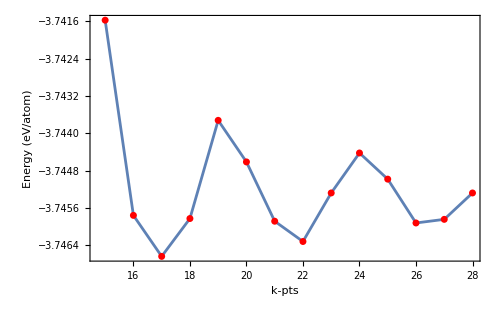

```mathematica
datakp //ListPlot[#,
Frame ->True,
FrameLabel->{"k-pts", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

Let' s obtain a convergence window to find the optimal kpoints .

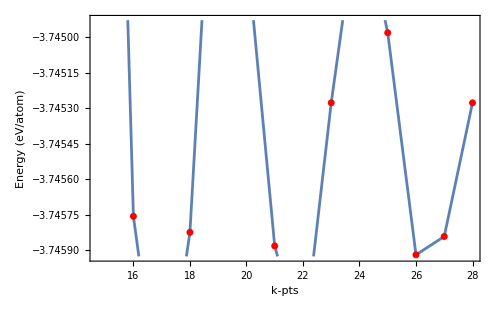

```mathematica
datakp //ListPlot[#,
Frame ->True,
FrameLabel->{"k-pts", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->{#[[-1,2]]-0.65*10^-3,#[[-1,2] ]+0.35 10^-3},
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

In general, the idea is to generate a convergence window of 1 mEv/atomsuch that it encloses the maximum number of kpoints (or any convergence parameter we want to review)!
25 KPTS!

### The EOS for fcc silicon

```mathematica
val = 16.5
```

16.5

```mathematica
Range[val-3,val+5,0.5]//Map[(#//ToString)<>" "&,#]&//StringJoin
```

13.5 14. 14.5 15. 15.5 16. 16.5 17. 17.5 18. 18.5 19. 19.5 20. 20.5 21. 21.5

```mathematica
cell = Import["cell.dat"]//Map[{#[[1]],#[[2]]}&,#]&;
```

```mathematica
cell//TableForm
```

13.5 | -3.55636
14. | -3.62266
14.5 | -3.67191
15. | -3.7067
15.5 | -3.7293
16. | -3.74161
16.5 | -3.74519
17. | -3.74142
17.5 | -3.73149
18. | -3.71639
18.5 | -3.69703
19. | -3.67418
19.5 | -3.64844
20. | -3.62016
20.5 | -3.58992
21. | -3.55808
21.5 | -3.52499

```mathematica
eos=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)))
```

e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0')

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm[v]
```

1.7377+923.257/v^2-55.3327/v^(4/3)-48.9754/v^(2/3)

```mathematica
nlm["BestFitParameters"]
```

{k[1]→1.7377,k[2]→-48.9754,k[3]→-55.3327,k[4]→923.257}

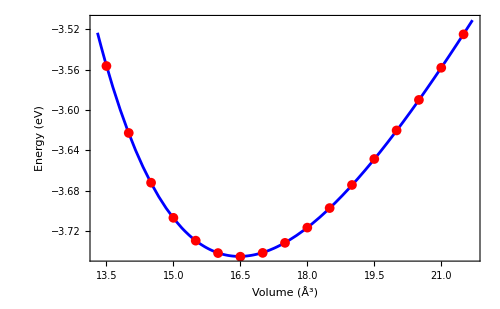

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2, (cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}]
```

```mathematica
nlm["RSquared"]
```

1.

```mathematica
opvol=FindMinimum[nlm[v],{v,16,17}]
```

{-3.74488,{v→16.4757}}

To get the lattice parameter in this system we have:

The bulk modulus B_0 is:

```mathematica
bulkm = v D[nlm[v],{v,2}]/.opvol[[2]]
```

0.479293

```mathematica
UnitConvert[Quantity[bulkm, "Electronvolts"/("Angstroms")^3], "GigaPascals"]
```

76.7912 GPa

```mathematica
-v/bulkm D[v D[nlm//Normal,{v,2}],v]/.opvol[[2]]
```

4.76571

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-3.74488,B0→0.479293,B'→4.76571,v0→16.4757}}

The cohesion energy in [eV] for Si fcc si predicted to be

```mathematica
e[bulk]/n-e[atom] /.{e[bulk]-> -10.84807047, e[atom]-> -0.88363161, n->2}
```

-4.5404

```mathematica
input=Import["DOSCAR", "Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

5.66955

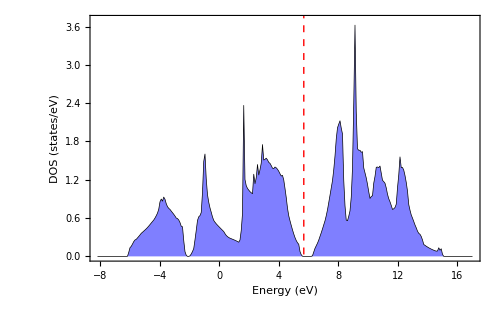

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
GridLines->{{ef}, None},
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{All, {0,3.7}}]
```

```mathematica
interp=Interpolation[dos]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[interp[x],{x,-8,ef}]
```

8.05949

Here we are going to analyze de partial density of states (PDOS), the arrange of the data PDOS is according to the AO:
energy,  s,  p_y p_z p_x d_{xy} d_{yz} d_{z2-r2} d_{xz} d_{x2-y2}

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
dos2=input[[7+300+2+300+2;;7+300+2+300+2+300]];
```

```mathematica
dosall=(dos1+dos2)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
f[d]=Map[{#[[1]],Plus@@(#[[6;;10]])}&,#]&;
f[py]=Map[{#[[1]],#[[3]]}&,#]&;
f[pz]=Map[{#[[1]],#[[4]]}&,#]&;
f[px]=Map[{#[[1]],#[[5]]}&,#]&;
```

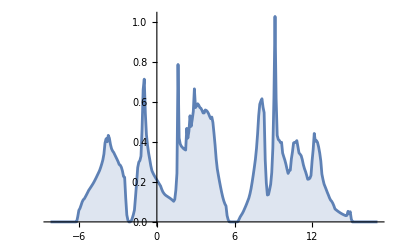

```mathematica
dosall//f[total]//ListPlot[#,Joined->True,Filling->Axis]&
```

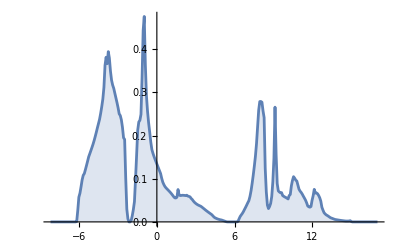

```mathematica
dosall//f[s]//ListPlot[#,Joined->True,Filling->Axis]&
```

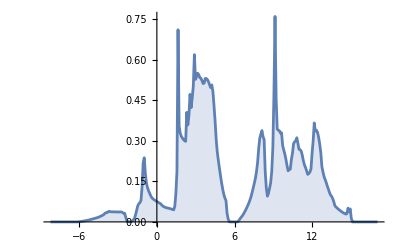

```mathematica
dosall//f[p]//ListPlot[#,Joined->True,Filling->Axis]&
```

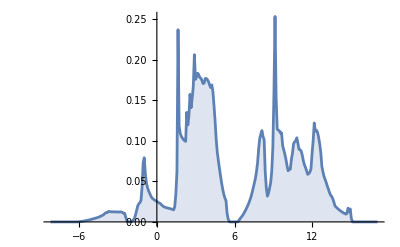

```mathematica
dosall//f[py]//ListPlot[#,Joined->True,Filling->Axis]&
```

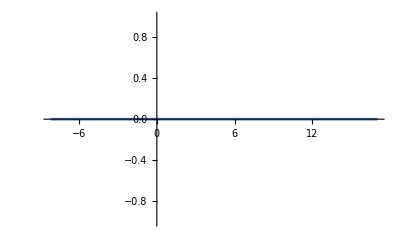

```mathematica
dosall//f[d]//ListPlot[#,Joined->True,Filling->Axis]&
```

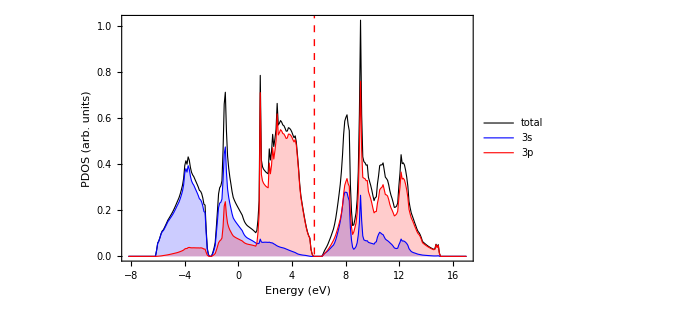

```mathematica
{dosall//f[total],dosall//f[s], dosall//f[p] }//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis},
Frame->True,
PlotRange->All,
PlotLegends->Placed[{"total", "3s", "3p"}, {Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1.0]],
PlotStyle->{{AbsoluteThickness[0.8], Black}, {AbsoluteThickness[0.8], Blue}, {AbsoluteThickness[0.8], Red}},
FrameLabel->{"Energy (eV)", "PDOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]&
```

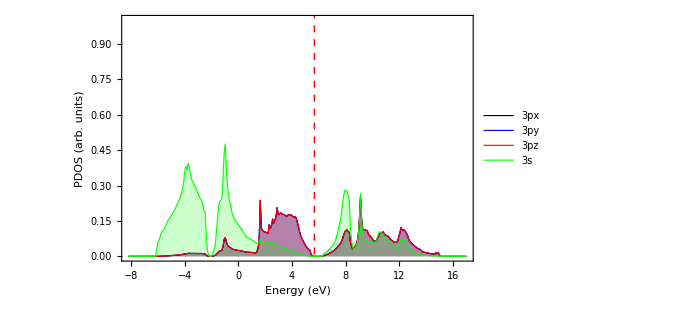

```mathematica
{dosall//f[px],dosall//f[py], dosall//f[pz],dosall//f[s] }//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{1->Axis, 2->Axis,3->Axis, 4->Axis},
Frame->True,
PlotRange->{Automatic,{0,1}},
PlotLegends->Placed[{"3px", "3py", "3pz","3s"}, {Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1.0]],
PlotStyle->{{AbsoluteThickness[0.8], Black}, {AbsoluteThickness[0.8], Blue}, {AbsoluteThickness[0.8], Red},{AbsoluteThickness[0.8], Green}},
FrameLabel->{"Energy (eV)", "PDOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]&
```

### Band Structure from PROCAR_OPT Along Path L→Γ→X→K→Γ @Henry Pinto, YTU

The following notebook will allow you to create the band structure from any VASP calculation that produces a PROCAR_OPT file

To run this notebook, be sure you have  in same directory  PROCAR_OPT and KPOINTS_OPT.

%%%% you can run the lines below %%%%%%%%%

```mathematica
Run["grep k-point PROCAR_OPT > kpt"];
Run["sed 's/-/ -/g' kpt > kpt2"];
Run["sed 's/k -point/k-point/g' kpt2 > kpts"];
Run["rm kpt kpt2"];
Run["grep band PROCAR_OPT > bandData"];
Run["grep \"# of bands\" PROCAR_OPT | tail -1 > numbands"];
```

```mathematica
(*define the Fermi elevel take from previous calculations OUTCAR.st*)
ef=input[[6,4]];
```

```mathematica
(*This gets number of kp and bands*)
bandsinfo=Import["numbands","Table"][[1]];
{Nkpt,Nbands}=bandsinfo//{#[[4]],#[[8]]}&
```

{140,8}

```mathematica
(*This gets the high symmetry points and divisions*)
path=Import["KPOINTS-bs","Table"];
div=path[[2,1]];
```

```mathematica
(*This defines the high symmetry points labels and the length*)
hsympts=(If[(path[[5]]//Length)==4,path[[5;;-1]]//Flatten//Partition[#,4]&//#[[All,4]]&, path[[5;;-1]]//Flatten//Partition[#,5]&//#[[All,5]]&]//Drop[#,{3,Length[#],2}]&)/."GAMMA"->"Γ"
NumGridL=(hsympts//Length)-2;
```

{L,Γ,X,K,Γ}

```mathematica
(*This defines the band energies shifted to Ef*)
bands=Import["bandData","Table"][[2;;Nbands Nkpt+1]][[All,5]]-ef//Partition[#,Nbands]&;
bandener=bands//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This defines k-point coordinates*)
kp=Import["kpts","Table"][[2;;Nkpt+1]][[All,{4,5,6}]];
kpt=kp//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This liniarizes k-point coordinates in 1D*)
kpt2=Join[{0},Table[Norm[kpt[[i+1]]-kpt[[i]]],{i,(kpt//Length)-1}]]//Accumulate;
```

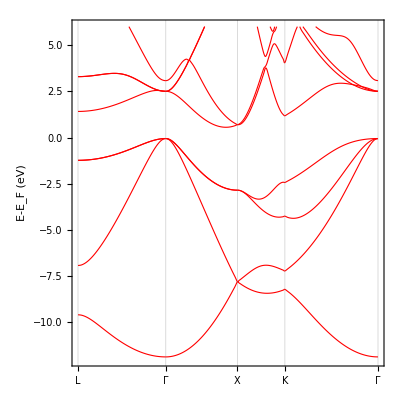

```mathematica
(*This creates the bands in kpt2 domain*)
bands2={kpt2,bandener}//Transpose;
Do[bd[i]=bands2//Map[{#[[1]],#[[2,i]]}&,#]&,{i,Nbands}];

(*please provide the bands you want to plot*)
ListPlot[Table[bd[i],{i,1,8(*Nbands*)}],
Frame->True,
FrameLabel->{"","E-E_F (eV)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->14},
Joined->True,
InterpolationOrder->2,
AspectRatio->1,
AxesStyle->Directive[Black,Dashed, AbsoluteThickness[0.7]],
FrameTicks->{{Automatic,None},{{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],hsympts}//Transpose,None}},
GridLines->{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],None},
PlotStyle->Directive[Red,AbsoluteThickness[0.8]],
PlotRange->{{0,kpt2[[-1]]},{-12,6}}]
```

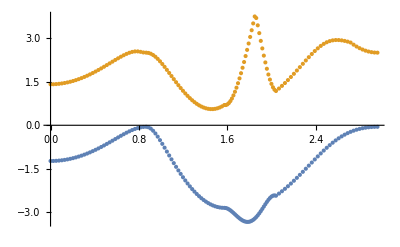

```mathematica
{bd[4],bd[5]}//ListPlot
```

Here we can see the valence band edge and the conductor band edge.

```mathematica
valBand = Interpolation[bd[4]]
```

InterpolatingFunction[…]

```mathematica
condBand = Interpolation[bd[5]]
```

InterpolatingFunction[…]

```mathematica
FindMaximum[valBand[x],{x,0.7}]
```

{-0.0528128,{x→0.860019}}

```mathematica
FindMinimum[condBand[x],{x,1.4}]
```

{0.556632,{x→1.45916}}

```mathematica
bandGap = 0.5566324240957816-(-0.052812811235963375)
```

0.609445

### Visualization of CHGCAR.vasp

In the following image, we display the iso-density of the valence electrons, notice the distribution.

And

### PDOS

```mathematica
input=Import["DOSCAR-bulk", "Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

9.03194

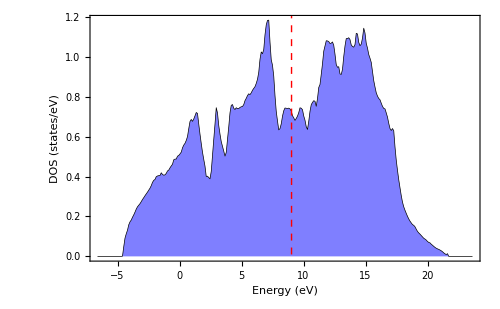

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
GridLines->{{ef}, None},
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All]
```

```mathematica
interp=Interpolation[dos]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[interp[x],{x,-8,ef}]
```

InterpolatingFunction::dmvali: The integration endpoint -8 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

7.99965

Here we are going to analyze de partial density of states (PDOS), the arrange of the data PDOS is according to the AO:
energy,  s,  p_y p_z p_x d_{xy} d_{yz} d_{z2-r2} d_{xz} d_{x2-y2}

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
dos2=input[[7+300+2+300+2;;7+300+2+300+2+300]];
```

```mathematica
dosall=(dos1+dos2)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
f[d]=Map[{#[[1]],Plus@@(#[[6;;10]])}&,#]&;
f[py]=Map[{#[[1]],#[[3]]}&,#]&;
f[pz]=Map[{#[[1]],#[[4]]}&,#]&;
f[px]=Map[{#[[1]],#[[5]]}&,#]&;
```

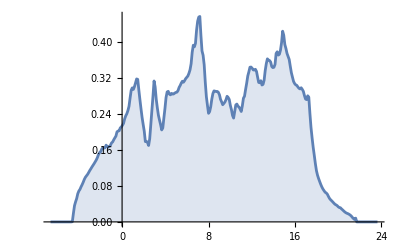

```mathematica
dosall//f[total]//ListPlot[#,Joined->True,Filling->Axis]&
```

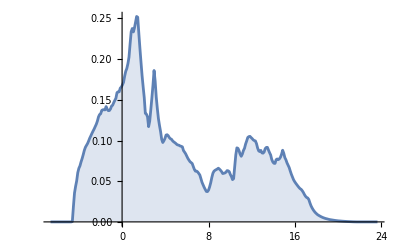

```mathematica
dosall//f[s]//ListPlot[#,Joined->True,Filling->Axis]&
```

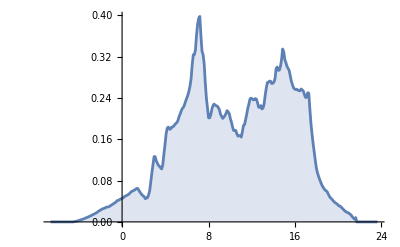

```mathematica
dosall//f[p]//ListPlot[#,Joined->True,Filling->Axis]&
```

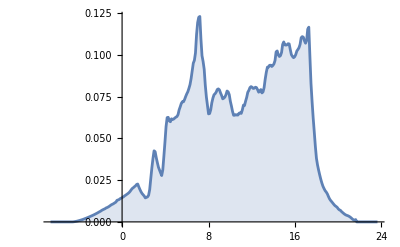

```mathematica
dosall//f[py]//ListPlot[#,Joined->True,Filling->Axis]&
```

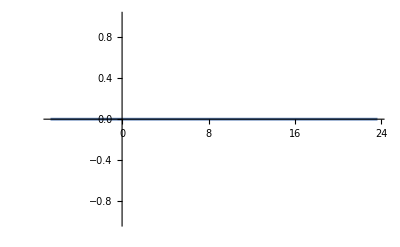

```mathematica
dosall//f[d]//ListPlot[#,Joined->True,Filling->Axis]&
```

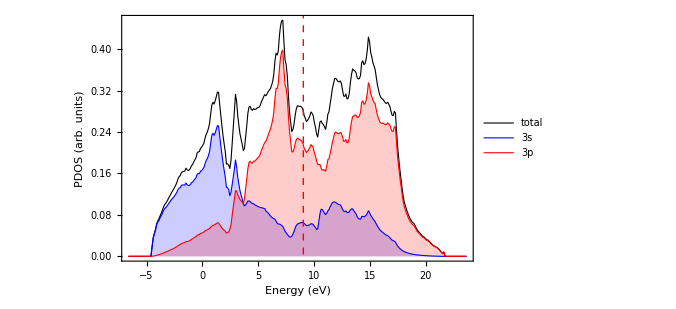

```mathematica
{dosall//f[total],dosall//f[s], dosall//f[p] }//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis},
Frame->True,
PlotRange->All,
PlotLegends->Placed[{"total", "3s", "3p"}, {Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1.0]],
PlotStyle->{{AbsoluteThickness[0.8], Black}, {AbsoluteThickness[0.8], Blue}, {AbsoluteThickness[0.8], Red}},
FrameLabel->{"Energy (eV)", "PDOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]&
```

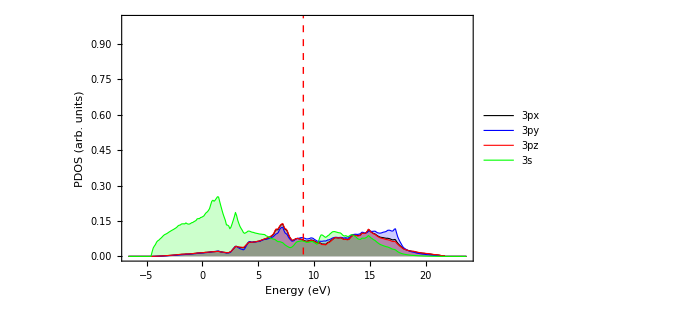

```mathematica
{dosall//f[px],dosall//f[py], dosall//f[pz],dosall//f[s] }//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{1->Axis, 2->Axis,3->Axis, 4->Axis},
Frame->True,
PlotRange->{Automatic,{0,1}},
PlotLegends->Placed[{"3px", "3py", "3pz","3s"}, {Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1.0]],
PlotStyle->{{AbsoluteThickness[0.8], Black}, {AbsoluteThickness[0.8], Blue}, {AbsoluteThickness[0.8], Red},{AbsoluteThickness[0.8], Green}},
FrameLabel->{"Energy (eV)", "PDOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]&
```

### Band Structure from PROCAR_OPT Along Path L→Γ→X→K→Γ @Henry Pinto, YTU

The following notebook will allow you to create the band structure from any VASP calculation that produces a PROCAR_OPT file

To run this notebook, be sure you have  in same directory  PROCAR_OPT and KPOINTS_OPT.

%%%% you can run the lines below %%%%%%%%%

```mathematica
Run["grep k-point PROCAR_OPT > kpt"];
Run["sed 's/-/ -/g' kpt > kpt2"];
Run["sed 's/k -point/k-point/g' kpt2 > kpts"];
Run["rm kpt kpt2"];
Run["grep band PROCAR_OPT > bandData"];
Run["grep \"# of bands\" PROCAR_OPT | tail -1 > numbands"];
```

```mathematica
(*define the Fermi elevel take from previous calculations OUTCAR.st*)
ef=input[[6,4]];
```

```mathematica
(*This gets number of kp and bands*)
bandsinfo=Import["numbands","Table"][[1]];
{Nkpt,Nbands}=bandsinfo//{#[[4]],#[[8]]}&
```

{140,8}

```mathematica
(*This gets the high symmetry points and divisions*)
path=Import["KPOINTS-bs","Table"];
div=path[[2,1]];
```

```mathematica
(*This defines the high symmetry points labels and the length*)
hsympts=(If[(path[[5]]//Length)==4,path[[5;;-1]]//Flatten//Partition[#,4]&//#[[All,4]]&, path[[5;;-1]]//Flatten//Partition[#,5]&//#[[All,5]]&]//Drop[#,{3,Length[#],2}]&)/."GAMMA"->"Γ"
NumGridL=(hsympts//Length)-2;
```

{L,Γ,X,K,Γ}

```mathematica
(*This defines the band energies shifted to Ef*)
bands=Import["bandData","Table"][[2;;Nbands Nkpt+1]][[All,5]]-ef//Partition[#,Nbands]&;
bandener=bands//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This defines k-point coordinates*)
kp=Import["kpts","Table"][[2;;Nkpt+1]][[All,{4,5,6}]];
kpt=kp//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This liniarizes k-point coordinates in 1D*)
kpt2=Join[{0},Table[Norm[kpt[[i+1]]-kpt[[i]]],{i,(kpt//Length)-1}]]//Accumulate;
```

```mathematica
(*This creates the bands in kpt2 domain*)
bands2={kpt2,bandener}//Transpose;
Do[bd[i]=bands2//Map[{#[[1]],#[[2,i]]}&,#]&,{i,Nbands}];

(*please provide the bands you want to plot*)
ListPlot[Table[bd[i],{i,1,8(*Nbands*)}],
Frame->True,
FrameLabel->{"","E-E_F (eV)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->14},
Joined->True,
InterpolationOrder->2,
AspectRatio->1,
AxesStyle->Directive[Black,Dashed, AbsoluteThickness[0.7]],
FrameTicks->{{Automatic,None},{{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],hsympts}//Transpose,None}},
GridLines->{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],None},
PlotStyle->Directive[Red,AbsoluteThickness[0.8]],
PlotRange->{{0,kpt2[[-1]]},{-12,6}}]
```

-Graphics-

```mathematica
{bd[4],bd[5]}//ListPlot
```

-Graphics-

Here we can see the valence band edge and the conductor band edge.

```mathematica
valBand = Interpolation[bd[4]]
```

InterpolatingFunction[…]

```mathematica
condBand = Interpolation[bd[5]]
```

InterpolatingFunction[…]

```mathematica
FindMaximum[valBand[x],{x,0.7}]
```

{-0.0528128,{x→0.860019}}

```mathematica
FindMinimum[condBand[x],{x,1.4}]
```

{0.556632,{x→1.45916}}

```mathematica
bandGap = 0.5566324240957816-(-0.052812811235963375)
```

0.609445

### Visualization of CHGCAR.vasp

The cohesion energy for β-Sn Si is predicted to be

```mathematica
e[bulk]/n-e[atom] /.{e[bulk]-> -10.26738149, e[atom]-> -0.88363161, n->2}
```

-4.25006